```mathematica
G=NormalDistribution[0,√(π/2)];
```

```mathematica
S1=StableDistribution[0,2,0,0,(√π)/2];
```

```mathematica
S2=StableDistribution[0,1.75,0,0,(√π)/2 1.75/2];
```

```mathematica
S3=StableDistribution[0,1.5,0,0,(√π)/2 1.5/2];
```

```mathematica
Ns=1000000;
```

```mathematica
Nst=30*300;
runs=1000;
```

```mathematica
seed=12;
```

```mathematica
SeedRandom[seed];Gruns=RandomVariate[G,{runs,Nst}];
```

```mathematica
SeedRandom[seed];S1runs=RandomVariate[S1,{runs,Nst}];
```

```mathematica
SeedRandom[seed];S2runs=RandomVariate[S2,{runs,Nst}];
```

```mathematica
SeedRandom[seed];S3runs=RandomVariate[S3,{runs,Nst}];
```

```mathematica
f[list_,nmax_]:={MeanDeviation[Take[list,30]],MeanDeviation[Take[list,nmax]]};
```

```mathematica
GMAD=Transpose[Map[f[#,30]&,Gruns]];
```

```mathematica
S1MAD=Transpose[Map[f[#,30]&,S1runs]];
```

```mathematica
S2MAD=Transpose[Map[f[#,75]&,S2runs]];
```

```mathematica
S3MAD=Transpose[Map[f[#,1000]&,S3runs]];
```

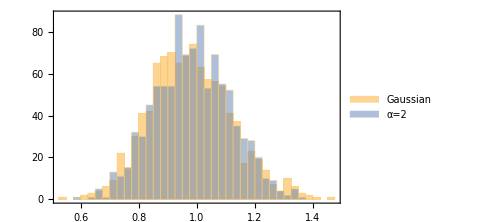

```mathematica
Histogram[{GMAD⟦1⟧,S1MAD⟦1⟧},{.025},Frame->True,ChartLegends->{"Gaussian","α=2"},ImageSize->Medium]
```

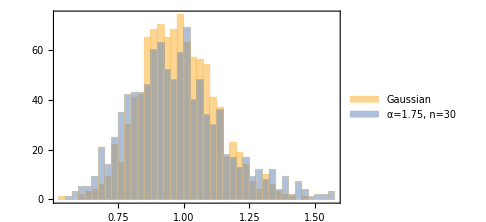
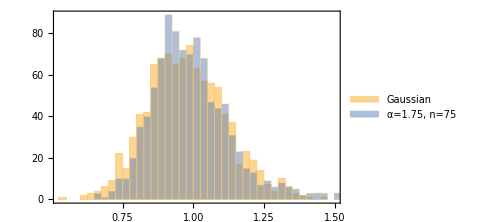

```mathematica
{Histogram[{GMAD⟦1⟧,S2MAD⟦1⟧},{.025},Frame->True,ChartLegends->{"Gaussian","α=1.75, n=30"},ImageSize->Medium],Histogram[{GMAD⟦1⟧,S2MAD⟦2⟧},{.025},Frame->True,ChartLegends->{"Gaussian","α=1.75, n=75"},ImageSize->Medium]}
```

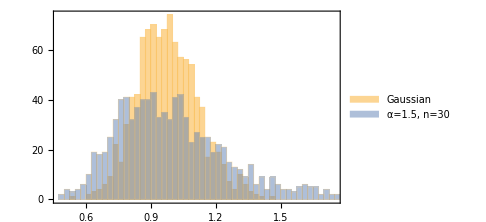
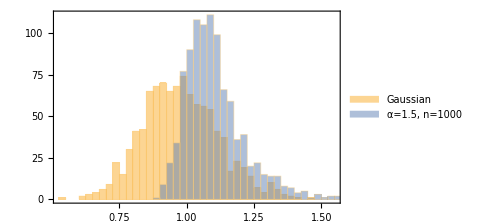

```mathematica
{Histogram[{GMAD⟦1⟧,S3MAD⟦1⟧},{.025},Frame->True,ChartLegends->{"Gaussian","α=1.5, n=30"},ImageSize->Medium],Histogram[{GMAD⟦1⟧,S3MAD⟦2⟧},{.025},Frame->True,ChartLegends->{"Gaussian","α=1.5, n=1000"},ImageSize->Medium]}
```

```mathematica
SeedRandom[seed];Gdata=RandomVariate[G,Ns];
```

```mathematica
SeedRandom[seed];S1data=RandomVariate[S1,Ns];
```

```mathematica
SeedRandom[seed];S2data=RandomVariate[S2,Ns];
```

```mathematica
SeedRandom[seed];S3data=RandomVariate[S3,Ns];
```

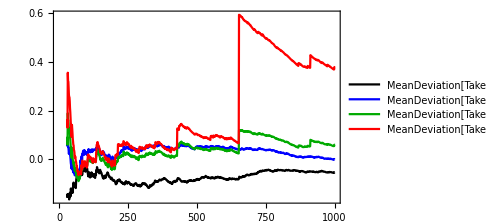

```mathematica
DiscretePlot[{
MeanDeviation[Take[Gdata,n]]-1,
MeanDeviation[Take[S1data,n]]-1,
MeanDeviation[Take[S2data,n]]-1,
MeanDeviation[Take[S3data,n]]-1},{n,30,1000},Filling->None,PlotRange->All,Frame->True,PlotLegends->"Expressions",ImageSize->Medium,AxesOrigin->{0,0},PlotStyle->{Black,Blue,Darker[Green],Red},Joined->True]
```

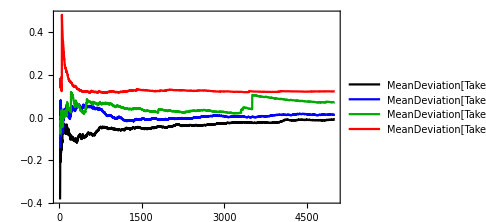

```mathematica
DiscretePlot[{
MeanDeviation[Take[Gdata,n]]-1,
MeanDeviation[Take[S1data,n]]-1,
MeanDeviation[Take[S2data,3n]]-1,
MeanDeviation[Take[S3data,200n]]-1},{n,20,5000},Filling->None,PlotRange->All,Frame->True,PlotLegends->"Expressions",ImageSize->Medium,AxesOrigin->{0,0},PlotStyle->{Black,Blue,Darker[Green],Red},Joined->True]
```